```mathematica
f[r_,Q_] = 1-2/r+Q^2/r^2;
```

```mathematica
rr[Q_]=r/.Solve[f[r,Q]==0,r]
```

{1-√(1-Q^2),1+√(1-Q^2)}

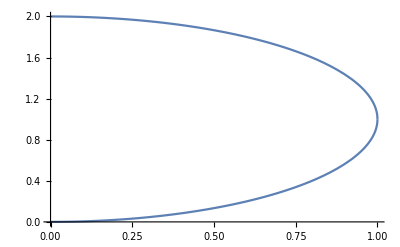

```mathematica
Plot[rr[Q],{Q,0,1}]
```

```mathematica
f[r_,α_] := 1 - (2(1+α))/r+(α(1+α))/r^2
```

```mathematica
U[r_,α_,ω_,L_] := α/r - Sqrt[f[r,α] (1+((L - ω(r^2-α(1+α)))^2)/r^2)]
```

```mathematica
l:=Solve[D[U[r,α,ω,L],r]==0,{L}][[1]]
```